```mathematica
a[θ_,ni_,nf_]:=(ni Sin[θ]/nf)/(√(1-(ni Sin[θ]/nf)^2))
b[θ_,ni_,nf_,d_]:=d Tan[θ]
r[ϕ_,θ_,ni_,nf_,d_]:=b[θ,ni,nf,d]/(Sin[ϕ]-a[θ,ni,nf]Cos[ϕ])
y[x_,θ_,ni_,nf_,d_]:=a[θ,ni,nf]x+b[θ,ni,nf,d]
```

```mathematica
getParaxial[ni_,nf_]:=nf/ni
getDerWavefront[ni_,nf_]:=-ni/(nf (-1+√((nf^2-ni^2)/nf^2)))
getLeastConfusion[na_,ni_,nf_,dcs_]:=-(x/.NSolve[-((((dcs na)/(√(1-na^2/nf^2) nf)+(na ni x)/(nf^2 √(1-(na^2 ni^2)/nf^4)))√(nf^2-ni^2))/(dcs nf))^(2/3)+((-ni x)/(dcs nf))^(2/3)==1,x][[1]])/dcs
```

```mathematica
getϵmin[nr_]:=-(-140 nr-42 nr^3-42 nr^5-15 nr^7)/(140+84 nr^2+15 nr^4)
```

```mathematica
getWmin[nr_]:=-(-3 π (√(-1+nr^2)+nr^2 ArcCsc[nr])+8 (nr+nr^3) EllipticE[1/nr^2]-8 nr (-1+nr^2) EllipticK[1/nr^2])/(2 (1-9 nr^2+6 nr^2 √(-1+nr^2) ArcCsc[nr]+3 nr^4 ArcCsc[nr]^2))
getWminapprox[nr_]:=(nr^3 (37+170 nr^2))/(7+60 nr^2+140 nr^4)
```

```mathematica
E(ϕ|m)=∫_0^ϕ (1-m sin^2(θ))^(1/2)ⅆθ
```

```mathematica
Assuming[ϵ∈Reals,Series[ArcCsc[1+ϵ],{ϵ,0,2}]]
```

π/2-√2 √ϵ+(5 ϵ^(3/2))/(6 √2)+O[ϵ]^(5/2)

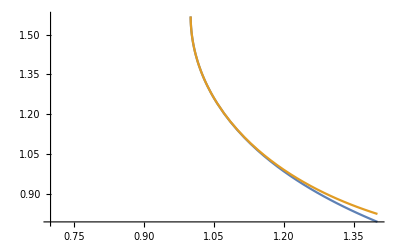

```mathematica
Plot[{ArcCsc[x],π/2-√2 √(x-1)+(5 (x-1)^(3/2))/(6 √2)},{x,0.7,1.4}]
```

```mathematica
With[{nf=1.518,ni=1.33,na =1.49,dcs=5,numθ=25,α=3.5,pry=10},{
getParaxial[ni,nf],
getWminapprox[nf/ni],
getϵmin[nf/ni],
getWmin[nf/ni],
getLeastConfusion[ni,ni,nf,dcs],
getDerWavefront[ni,nf],
getLeastConfusion[na,ni,nf,dcs]}]
```

{1.14135,1.19068,1.24211,1.34421,1.41355,1.69152,2.40854}

```mathematica
With[{nf=1.518,ni=1.33},(nf/ni)^3]
```

1.48683

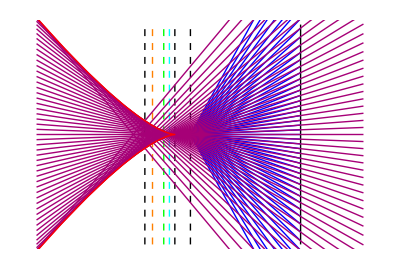

```mathematica
With[{nf=1.518,ni=1.33,na =1.33 (*1.49*),dcs=50,numθ=25,α=2.},
Block[{pry=1*dcs,θimax,θilist,θflist,αnp,αpar,αderW,αϵ,prxm,prxp,αlc,αWmin,αWminapprox},
prxm=-(.1+α)nf dcs/ni;
prxp=-(1.5-α)nf dcs/ni;
θimax=ArcSin[na/nf];
θilist=Join[Table[θ,{θ,-θimax,-θimax/numθ,θimax/numθ}],Table[θ,{θ,θimax/numθ,θimax,θimax/numθ}]];
θflist=ArcSin[ni/nf Sin[#]]&/@θilist;
αlc =getLeastConfusion[na,ni,nf,dcs];
αpar=getParaxial[ni,nf];
αderW=getDerWavefront[ni,nf];
αϵ=getϵmin[nf/ni];
αWmin=getWmin[nf/ni];
αWminapprox=getWminapprox[nf/ni];
Show[{
Graphics[{
{{Thick,Line[{{0,-pry},{0,pry}}]},Dashed,
Line[{{-dcs,-pry},{-dcs,pry}}],
Line[{{-αpar dcs,-pry},{-αpar dcs,pry}}],(*Line[{{-αderW dcs,-pry},{-αderW dcs,pry}}],*)
Line[{{-αlc dcs,-pry},{-αlc dcs,pry}}],
Green,Line[{{-αϵ dcs,-pry},{-αϵ dcs,pry}}],Orange,Line[{{-αWmin dcs,-pry},{-αWmin dcs,pry}}],Cyan,Line[{{-αWminapprox dcs,-pry},{-αWminapprox dcs,pry}}]},{Blue,Thin,Line[{{-dcs,0},{0,0}}],Line[{{-dcs,0},{0,dcs Tan[#]}}]&/@θilist},
{Hue[0.88,1.,0.65], Thin, Line[{{prxm,0},{prxp,0}}],Line[{{prxm,y[prxm,#,ni,nf,dcs]},{prxp,y[prxp,#,ni,nf,dcs]}}]&/@θilist}}
],
ParametricPlot[{(-dcs nf)/ni Cosh[θ]^3,(dcs nf)/(√(nf^2-ni^2))Sinh[θ]^3},{θ,-π/2,π/2},PlotStyle->{Red,Thick}]}
,PlotRange->{{prxm,prxp},{-pry,pry}}]
]]
```

```mathematica
abeW[u_,nr_,α_]:=1/nr √(1-( nr u)^2)+ α √(1-u^2)
approxW[u_,nr_,α_]:=1/nr+α-1/2(nr+α)u^2-1/8(nr^3+α)u^4
```

## Least wavefront aberration

```mathematica
Wmean[α_,nr_]=Assuming[{nr>1,α∈Reals},nr Integrate[abeW[u,nr,α],{u,0,1/nr}]]
```

(π+2 √(-1+nr^2) α+2 nr^2 α ArcCsc[nr])/(4 nr)

```mathematica
W2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[(abeW[u,nr,α] )^2 ,{u,0,1/nr}]]
```

ConditionalExpression[(2+(-1+3 nr^2) α^2+2 nr α ((1+nr^2) EllipticE[1/nr^2]-(-1+nr^2) EllipticK[1/nr^2]))/(3 nr^3), Re[nr]>1&&Im[nr]==0]

```mathematica
With[{nr=1.518/1.33},
Manipulate[Plot[{abeW[u,nr,α], Wmean[α,nr]},{u,0,1/nr}],{α,-2,0}]]
```

```mathematica
Assuming[{nr>1,α∈Reals},D[(nr W2mean[α,nr]-Wmean[α,nr]^2),α]//Simplify]
```

```mathematica
Solve[1/(24 nr^2)(16 (-1+3 nr^2) α-6 (√(-1+nr^2)+nr^2 ArcCsc[nr]) (π+2 √(-1+nr^2) α+2 nr^2 α ArcCsc[nr])+16 nr ((1+nr^2) EllipticE[1/nr^2]-(-1+nr^2) EllipticK[1/nr^2]))==0,α]//Simplify
```

{{α→(-3 π (√(-1+nr^2)+nr^2 ArcCsc[nr])+8 (nr+nr^3) EllipticE[1/nr^2]-8 nr (-1+nr^2) EllipticK[1/nr^2])/(2 (1-9 nr^2+6 nr^2 √(-1+nr^2) ArcCsc[nr]+3 nr^4 ArcCsc[nr]^2))}}

```mathematica
approxWmean[α_,nr_]=Assuming[{nr>1,α∈Reals},nr Integrate[approxW[u,nr,α],{u,0,1/nr}]]
approxW2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[(approxW[u,nr,α] )^2 ,{u,0,1/nr}]]
```

nr ((-nr-α)/(6 nr^3)+(-nr^3-α)/(40 nr^5)+(1/nr+α)/nr)

2767/(4032 nr^3)-(289 α)/(10080 nr^6)-(181 α)/(840 nr^4)+(97 α)/(60 nr^2)+α^2/(576 nr^9)+α^2/(56 nr^7)-α^2/(3 nr^3)+α^2/nr

```mathematica
Assuming[{nr>1,α∈Reals},D[(nr approxW2mean[α,nr]-approxWmean[α,nr]^2),α]//Simplify]
```

```mathematica
Solve[(37 nr^3+170 nr^5+7 α+60 nr^2 α+140 nr^4 α)/(3150 nr^8)==0,α]
```

{{α→-(nr^3 (37+170 nr^2))/(7+60 nr^2+140 nr^4)}}

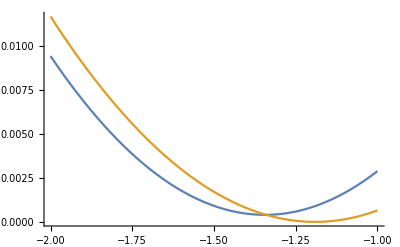

```mathematica
With[{nr=1.518/1.33},Plot[{(nr W2mean[α,nr]-Wmean[α,nr]^2),(nr approxW2mean[α,nr]-approxWmean[α,nr]^2)},{α,-2,-1}]]
```

## Least spot size

```mathematica
D[abeW[√(x^2+y^2),nr,α],x]
```

-(nr x)/(√(1-nr^2 (x^2+y^2)))-(x α)/(√(1-x^2-y^2))

```mathematica
Integrate[Integrate[(-(nr u Cos[ϕ])/(√(1-nr^2 u^2))-(u Cos[ϕ] α)/(√(1-u^2)))^2 u,{ϕ,0,2π}],{u,0,nr}]
```

$Aborted

```mathematica
D[abeW[u,nr,α],u]
```

-(nr u)/(√(1-nr^2 u^2))-(u α)/(√(1-u^2))

```mathematica
Integrate[D[abeW[u,nf,ni,α],u]^2 u,{u,0,ni/nf}]
```

ConditionalExpression[-(2 ni^3+nf ni^2 √(1-ni^2/nf^2) α+2 nf^3 (-1+√(1-ni^2/nf^2)) α)/(3 nf^2), Im[nf]==0&&Im[ni]==0&&((Re[ni]>0&&Re[nf]≥ni)||(Re[ni]<0&&Re[nf]≤ni))]

```mathematica
Integrate[(Tan[q]/Tan[ ArcSin[ni/nf Sin[q]]]),{q,0,ArcSin[ni/nf]}]/ArcSin[ni/nf]
```

$Aborted

```mathematica
w20 [nf_,ni_][u_]:=(2nf)/ni (ni-nf)(1-√(1-u^2))/2
w40[nf_,ni_][u_]:=(2 nf^2)/ni^3 (ni^2-nf^2)((1-√(1-u^2))/2)^2
def[nf_,zf_][u_]:=nf zf √(1-u^2)
```

```mathematica
(def[nf,nf/ni-(nf/ni)^3][u]+w20 [nf,ni][u]+w40[nf,ni][u])//Simplify
```

(nf (nf-ni) (nf^2 (-2+u^2)+nf ni (-2+u^2)+2 ni^2 (-1+√(1-u^2))))/(2 ni^3)

```mathematica
With[{nf=1.518,ni=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=1.2,pry=2},
Manipulate[Plot[def[nf,zf][u]+w20 [nf,ni][u]+w40[nf,ni][u],{u,0,1.49/1.518}]
,{zf,-1,0}]]
```

```mathematica
D[def[nf,zf][u]+w20 [nf,ni][u]+w40[nf,ni][u],u]/.{zf->(nf/ni)^2}//Simplify
```

(nf u (-nf^2 ni+ni^3-nf ni^2 √(1-u^2)+nf^3 (-1+√(1-u^2))))/(ni^3 √(1-u^2))

```mathematica
D[def[nf,zf][u]+w20 [nf,ni][u]+w40[nf,ni][u],{u,2}]/.{u->0}
```

(nf (-nf+ni))/ni-nf zf

```mathematica
With[{nf=1.518,ni=1.33},(-nf+ni/ni)]
```

-0.518

```mathematica
With[{nf=1.518,ni=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=1.2,pry=2},
Manipulate[Plot[(nf (-nf+ni) u)/(ni √(1-u^2))+(nf^2 (-nf^2+ni^2) u (1-√(1-u^2)))/(ni^3 √(1-u^2))-(nf u zf)/(√(1-u^2)),{u,0,1.49/1.518}]
,{zf,-1,0}]]
```

```mathematica
With[{nf=1.518,ni=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,pry=2},
Manipulate[Plot[{nf/ni √(1-(nf/ni u)^2)-α √(1-u^2),-(nf^3 u)/(ni^3 √(1-(nf^2 u^2)/ni^2))+(u α)/(√(1-u^2))},{u,0,ni/nf +0 1.49/1.518}]
,{α,1,2}]]
```

```mathematica
Integrate[nf/ni √(1-(nf/ni u)^2)-α √(1-u^2),{u,0,ni/nf}]
```

ConditionalExpression[1/4 (π-2 α ((nm √(1-nm^2/ni^2))/ni+ArcSin[nm/ni])), Re[ni/nm]>1||Re[ni/nm]<-1||ni/nm∉ℝ]

```mathematica
D[nf/ni √(1-(nf/ni u)^2)-α √(1-u^2),{u,1}]
```

-(ni^3 u)/(nm^3 √(1-(ni^2 u^2)/nm^2))+(u α)/(√(1-u^2))

```mathematica
With[{nf=1.518,ni=1.33},{nf/ni,nf^3/ni^3}]
```

{1.14135,1.48683}

```mathematica
NIntegrate[(Tan[q]/Tan[ ArcSin[1.33/1.518Sin[q]]]),{q,0,ArcSin[1.4/1.52]}]/ArcSin[1.4/1.52]-1
```

0.261176

```mathematica
Series[√(1-u^2),{u,0,4}]
```

1-u^2/2-u^4/8+O[u]^5

```mathematica
Series[EllipticE[1+u],{u,0,1}]
```

Floor[-Arg[u]/(2 π)] ((ⅈ π u)/2+O[u]^2)+(1+1/4 ⅈ (-ⅈ+π+4 ⅈ Log[2]-ⅈ Log[u]) u+O[u]^2)

```mathematica
EllipticK[1/nr^2]
```

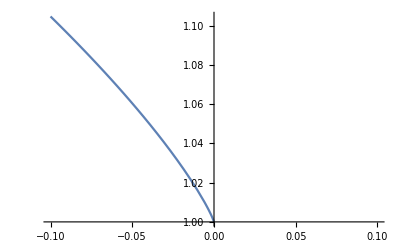

```mathematica
Plot[EllipticE[1+u],{u,-0.1,.1}]
```

```mathematica
EllipticK[0.92]
```

2.68355

```mathematica
D[(x^2+y^2)^2,x]
```

4 x (x^2+y^2)

```mathematica
Integrate[Integrate[(-(nr+α)u Cos[ϕ]-1/2(nr^3+α)u^3 Cos[ϕ])^2,{ϕ,0,2π}],{u,0,nr}]
```

```mathematica
D[1/3 nr^3 π (nr+α)^2+1/5 nr^5 π (nr+α) (nr^3+α)+1/28 nr^7 π (nr^3+α)^2,α]
```

```mathematica
Solve[2/3 nr^3 π (nr+α)+1/5 nr^5 π (nr+α)+1/5 nr^5 π (nr^3+α)+1/14 nr^7 π (nr^3+α)==0,α]
```

{{α→(-140 nr-42 nr^3-42 nr^5-15 nr^7)/(140+84 nr^2+15 nr^4)}}

```mathematica
With[{nr=1.2},{-nr,-(nr^3 (37+170 nr^2))/(7+60 nr^2+140 nr^4),(-140 nr-42 nr^3-42 nr^5-15 nr^7)/(140+84 nr^2+15 nr^4)}]
```

{-1.2,-1.26908,-1.36557}

```mathematica
Integrate[(-(nr u Cos[ϕ])/(√(1-nr^2 u^2))-(u Cos[ϕ] α)/(√(1-u^2)))^2 u,{ϕ,0,2π}]
```

π u^3 (nr/(√(1-nr^2 u^2))+α/(√(1-u^2)))^2

```mathematica
Assuming[{α∈Reals,nr>1},Integrate[u^3 (nr/(√(1-nr^2 u^2))+α/(√(1-u^2)))^2,{u,0,1/nr}]]
```

∫_0^(1/nr) u^3 (nr/(√(1-nr^2 u^2))+α/(√(1-u^2)))^2ⅆu